```mathematica
yt = 1;
y0 = 0;
sol = ParametricNDSolve[{y'[x] == yt-y[x-a], y[0]==0,WhenEvent[x-a<=0, y[x-a]==0]},y,{x,0,20},{a}]
```

{y→ParametricFunction[<>]}

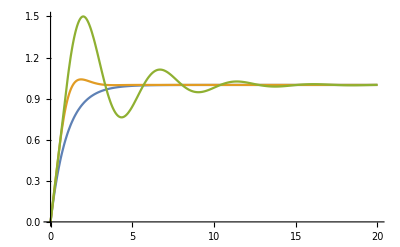

```mathematica
Plot[Evaluate[Table[y[a][x]/.sol,{a,0,1,.5}]],{x,0,20},PlotRange->All]
```